# Лабораторная работа по оптической микроскопии

Нехаев Александр, 652а гр.

13.09.2019

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[".\\2019-09-10"];
```

## Определение максимального достигнутого разрешения по Релею

Получили изображение одной из структур на поверхности используемого образца.

-Graphics-

Получили изображение той же структуры, но с UV фильтром

-Graphics-

## Гистограмма распределения по размерам частиц загрязнения

Получили изображение загрязненной части образца:

-Graphics-

Установим размер масштабирующего изображения

```mathematica
scale=ImageTrim[Import["3_x10_DF.png"],{{1884,20},{2028,60}}]
```

-Graphics-

```mathematica
scalingCoef=Quantity[50,"Micrometers"]/ImageDimensions[scale][[1]]
```

25/73 µm

Преобразуем изображение в черно-белое и обрежем ненужные фрагменты

```mathematica
image=ImageTrim[Binarize[Import["3_x10_DF.png"]],{{0,0},{1720,1544}}]
```

-Graphics-

Составим таблицу с описанием параметров (изображение, длина, ширина и площадь эллипса, которым производится аппроксимация пятна).

```mathematica
dataset=ComponentMeasurements[image,{"Image","Length","Width","Area"},All,"Dataset",CornerNeighbors->True]
```

Dataset[<>]

Составим массив из усредненных размеров частиц с учетом размерности.

```mathematica
dustArray=Around[Mean[{Values[ComponentMeasurements[image,"Length"]],Values[ComponentMeasurements[image,"Width"]]}],1]*scalingCoef;
```

По полученному массиву построим гистограмму

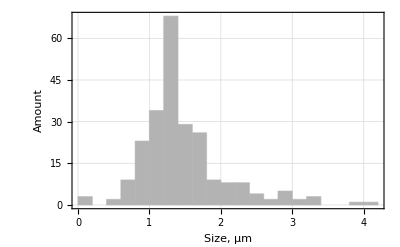

```mathematica
Histogram[dustArray,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Size, μm","Amount"}]
```